# Funciones de Bessel

Autora: Victoria Gómez Bifante

```mathematica
(*J(n,z) function Bessel)*)
```

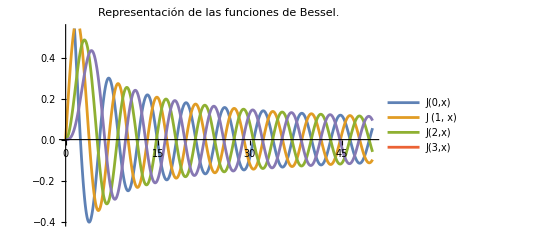

```mathematica
Plot[{BesselJ[0,x],BesselJ[1,x],BesselJ[2,x],,BesselJ[3,x]},{x,0,50}, FrameLabel->{"z" ,"Función de Bessel J(n,z)"}, PlotLabel-> "Representación de las funciones de Bessel.", PlotLegends->{" J(0,x) ", "J (1, x)", "J(2,x)", "J(3,x)"}]
```

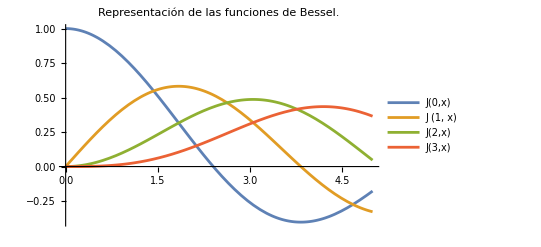

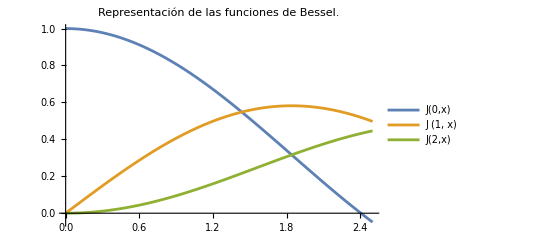

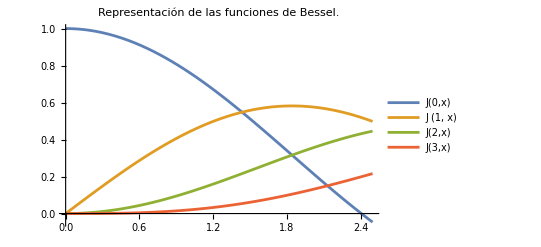

```mathematica
Plot[{BesselJ[0,x],BesselJ[1,x],BesselJ[2,x],BesselJ[3,x]},{x,0,5}, FrameLabel->{"z" ,"Función de Bessel J(n,z)"}, PlotLabel-> "Representación de las funciones de Bessel.", PlotLegends->{" J(0,x) ", "J (1, x)", "J(2,x)", "J(3,x)"}]
Plot[{BesselJ[0,x],BesselJ[1,x],BesselJ[2,x]},{x,0,2.5}, FrameLabel->{" z "," J(n.z)"} , PlotLabel-> "Representación de las funciones de Bessel.", PlotLegends->{" J(0,x) ", "J (1, x)", "J(2,x)"}]
Plot[{BesselJ[0,x],BesselJ[1,x],BesselJ[2,x],BesselJ[3,x]},{x,0,2.496}, FrameLabel->{"z" ,"Función de Bessel J(n,z)"}, PlotLabel-> "Representación de las funciones de Bessel.", PlotLegends->{" J(0,x) ", "J (1, x)", "J(2,x)", "J(3,x)"}]
```

```mathematica
f = BesselJ[1/2,x]* BesselY[1/2,3.3172*x] - BesselJ[1/2,3.3172*x]* BesselY[1/2,x];
g = BesselJ[2/2,x]* BesselY[2/2,3.3172*x] - BesselJ[2/2,3.3172*x]* BesselY[2/2,x];
```

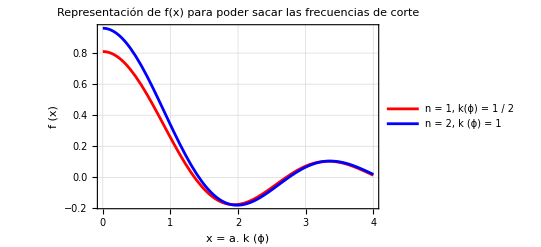

```mathematica
Plot[{f,g},{x,0,4}, PlotLegends->{" n = 1, k(ϕ) = 1 / 2 ","n = 2, k (ϕ) = 1 "}, PlotStyle->{Red ,Blue}, FrameLabel->{" x = a. k (ϕ) "," f (x)"}, PlotLabel-> "Representación de f(x) para poder sacar las frecuencias de corte", PlotTheme-> "FullAxesGrid"]
```